# Abductive reasoning

## Global conditions

```mathematica
Clear["Global`*"]
r=3;
ϵ=(1-e1)*(1-e2)+e1*e2;
e=e2;
(*ternary coords where x corresponds to freq alld, y to freq allc *)
TernCoords[x_,y_]={{1/2,-1/2},{-Tan[Pi/3]/2,-Tan[Pi/3]/2}}.{x,y}+{1/2,Tan[Pi/3]/2};
diskradius=.015;
textoffset=.05;
thickness=.005;
vlabels={Graphics[Text[Style["AllD",FontSize->Large],{-textoffset,-textoffset}]],Graphics[Text[Style["AllC",FontSize->Large],{1+textoffset,-textoffset}]],Graphics[Text[Style["Disc",FontSize->Large],{1/2,Tan[Pi/3]/2+textoffset}]]};
SetDirectory["/Users/brycemorsky"];
```

## Scoring

### Ternary plot

```mathematica
T=100000;
e1=0.01;
e2=0.01;
ψ=0.5;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* States 1 and 2: B ∅ *)
P1=0;
(* States 3 and 4: B -> *)
P31=(1-g)*ψ*e; 
P34=g*(1-ψ)*ϵ;
P3=FullSimplify[P34/(P31+P34)];
(* States 5 and 6: G ∅ *)
P51=(1-g)*(1-ψ)*(1-e); 
P54=g*ψ*(1-ϵ);
P5=FullSimplify[P54/(P51+P54)];
(* States 7 and 8: G -> *)
P7=1;
Qbd=(1-e)*P1+e*P3;
Qbc=ϵ*P3+(1-ϵ)*P1;
Qgd=(1-e)*P5+e*P7;
Qgc=ϵ*P7+(1-ϵ)*P5;
(*Qbd=0;
Qbc=0;
Qgd=1;
Qgc=1;*)
repsys={
gx'[t]==(1-gx[t])*Qbc - gx[t]*(1-Qgc),
gy'[t]==(1-gy[t])*Qbd - gy[t]*(1-Qgd),
gz'[t]==(1-gz[t])*(g*Qbc+(1-g)*Qbd)-gz[t]*(g*(1-Qgc)+(1-g)*(1-Qgd))
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,T}];
M[[count]]= {0.01*i,0.01*j,gx[T]/.R[[1]],gy[T]/.R[[1]],gz[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==Evaluate[(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]})],
y'[t]==Evaluate[(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]})],
gx'[t]==10000*Evaluate[((1-gx[t])*Qbc - gx[t]*(1-Qgc))/.{x->x[t],y->y[t]}],
gy'[t]==10000*Evaluate[((1-gy[t])*Qbd - gy[t]*(1-Qgd))/.{x->x[t],y->y[t]}],
gz'[t]==10000*Evaluate[((1-gz[t])*(g*Qbc+(1-g)*Qbd)-gz[t]*(g*(1-Qgc)+(1-g)*(1-Qgd)))/.{x->x[t],y->y[t]}]
};
Eqstable=Array[m,{4851,2}];
count = 1;
Do[
{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,T}][[1]];
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j,gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count]]= {Chop[x[T]/.R[[1]]],Chop[y[T]/.R[[1]]]};
count=count+1;
,{i,1,98},{j,1,99-i}];

(* Unstable equilibria *)
fullsysunstable={
x'[t]==Evaluate[(-x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]})],
y'[t]==Evaluate[(-y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]})],
gx'[t]==10000*Evaluate[((1-gx[t])*Qbc - gx[t]*(1-Qgc))/.{x->x[t],y->y[t]}],
gy'[t]==10000*Evaluate[((1-gy[t])*Qbd - gy[t]*(1-Qgd))/.{x->x[t],y->y[t]}],
gz'[t]==10000*Evaluate[((1-gz[t])*(g*Qbc+(1-g)*Qbd)-gz[t]*(g*(1-Qgc)+(1-g)*(1-Qgd)))/.{x->x[t],y->y[t]}]
};
Equnstable=Array[m,{10,2}];
count = 1;
Do[
{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsys/.{x->0.2*i,y->0.2*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,T}][[1]];
R=NDSolve[Join[fullsysunstable,{x[0]==0.2*i,y[0]==0.2*j,gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Equnstable[[count]]= {Chop[x[T]/.R[[1]]],Chop[y[T]/.R[[1]]]};
count=count+1;
,{i,1,4},{j,1,5-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0.2759856165880882,0.3804426112687108],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageScoring=Show[ternplot,dots,vlabels, ImageSize-> Large,PlotRangePadding->.1];;
Export["scoring_psi05.pdf",imageScoring];
```

$Aborted

```mathematica
sys={
0==Evaluate[(x*(pix-pi)/.{gx[t]->gx,gy[t]->gy,gz[t]->gz})],
0==Evaluate[(y*(piy-pi)/.{gx[t]->gx,gy[t]->gy,gz[t]->gz})],
0==10000*Evaluate[((1-gx[t])*Qbc - gx[t]*(1-Qgc))/.{gx[t]->gx,gy[t]->gy,gz[t]->gz}],
0==10000*Evaluate[((1-gy[t])*Qbd - gy[t]*(1-Qgd))/.{gx[t]->gx,gy[t]->gy,gz[t]->gz}],
0==10000*Evaluate[((1-gz[t])*(g*Qbc+(1-g)*Qbd)-gz[t]*(g*(1-Qgc)+(1-g)*(1-Qgd)))/.{gx[t]->gx,gy[t]->gy,gz[t]->gz}]
};
FindRoot[sys,{{x,0.2},{y,0.4},{gx,0.9},{gy,0.01},{gz,0.5}}]
```

{x→0.275986,y→0.380443,gx→0.9802,gy→0.01,gz→0.414226}

```mathematica
FindRoot[Join[sys,{0<x<1,0<y<1,0<gx<1,0<gy<1,0<gz<1}],{{x,0.5},{y,0.25},{gx,0.5},{gy,0.5},{gz,0.5}},Reals]
```

```mathematica
Eqstable
Equnstable
```

{{0,0.000603102},{0,0.000603102},{0,0.8121},{0,1.},{0,0.000603102},{0,0.812503},{0,1.},{0,0.80807},{0,1.},{0,1.}}

{{0.000621509,0},{0.000621509,0},{0.823048,0},{1.,0},{0.000621509,0},{0.823404,0},{1.,0},{0.819538,0},{1.,0},{1.,0}}

```mathematica
T=10000;
g=x*gx+y*gy+(1-x-y)*gz;
(* World 1: B ∅ *)
w1=0;
(* World 2: B -> *)
w21=(1-g)*ψ*e; 
w24=g*(1-ψ)*ϵ;
w2=FullSimplify[w24/(w21+w24)];
(* World 3: G ∅ *)
w31=(1-g)*(1-ψ)*(1-e); 
w34=g*ψ*(1-ϵ);
w3=FullSimplify[w34/(w31+w34)];
(* World 4: G -> *)
w4=1;
Qbd=(1-e)*w1+e*w2;
Qbc=ϵ*w2+(1-ϵ)*w1;
Qgd=(1-e)*w3+e*w4;
Qgc=ϵ*w4+(1-ϵ)*w3;
ψ=0.5;
(*Qbd=0;
Qbc=0;
Qgd=1;
Qgc=1;*)
repsys={
0==(1-gx)*Qbc - gx*(1-Qgc),
0==(1-gy)*Qbd - gy*(1-Qgd),
0==(1-gz)*(g*Qbc+(1-g)*Qbd)-gz*(g*(1-Qgc)+(1-g)*(1-Qgd))
}/.{e->0.01,e1->0.01,e2->0.01,ϵ-> 0.99^2+0.01^2};
M=Array[m,{5151,5}];
count=1;
Do[
M[[count]]= {0.01*i,0.01*j,gx,gy,gz}/.FindRoot[repsys/.{x->0.01*i,y->0.01*j},{{gx,0.9},{gy,0.1},{gz,0.6}}];
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==Evaluate[(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]})],
y'[t]==Evaluate[(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]})],
gx'[t]==10000*Evaluate[((1-gx)*Qbc - gx*(1-Qgc))/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}],
gy'[t]==10000*Evaluate[((1-gy)*Qbd - gy*(1-Qgd))/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}],
gz'[t]==10000*Evaluate[((1-gz)*(g*Qbc+(1-g)*Qbd)-gz*(g*(1-Qgc)+(1-g)*(1-Qgd)))/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}]
}/.{e->0.01,e1->0.01,e2->0.01,ϵ-> 0.99^2+0.01^2};
Eqstable=Array[m,{4851,2}];
count1 = 1;
Do[
(*{icgx,icgy,icgz}={gx,gy,gz}/.FindRoot[repsys/.{x->0.01*i,y->0.01*j},{{gx,0.95},{gy,0.01},{gz,0.7}}];*)
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count1]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count1=count1+1;
,{i,1,98},{j,1,99-i}];
N
dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageScoring=Show[ternplot,dots,vlabels, ImageSize-> Large,PlotRangePadding->.1];;
Export["scoring_psi05.pdf",imageScoring];
```

### Stability analysis

```mathematica
Clear["Global`*"]
(* States 1 and 2: B ∅ *)
P1=0;
(* States 3 and 4: B -> *)
P31=(1-g)*ψ*e; 
P34=g*(1-ψ)*ϵ;
P3=P34/(P31+P34);
(* States 5 and 6: G ∅ *)
P51=(1-g)*(1-ψ)*(1-e); 
P54=g*ψ*(1-ϵ);
P5=P54/(P51+P54);
(* States 7 and 8: G -> *)
P7=1;
Qbd=e*P3;
Qbc=ϵ*P3;
Qgd=(1-e)*P5+e;
Qgc=ϵ+(1-ϵ)*P5;
```

```mathematica
(* Reputations converge to 0 for ψ > ϵ/(1+ϵ-e) *)
FullSimplify[Qbc*(1-g)*g+Qbd*(1-g)^2+Qgc*g^2+Qgd*g*(1-g)-g/.{ψ->ϵ/(1+ϵ-e)}]
```

-((-1+e) (-1+g) g^2 (-1+e+ϵ) (-1+e^2 (-1+g)+g ϵ^2+e (1+ϵ-2 g ϵ)))/((-g+e (-1+2 g)) ((-1+e)^2 (-1+g)-g ϵ+g ϵ^2))

```mathematica
(* Stability analysis *)
FullSimplify[Together[(1-g)*Qbd-g*(1-Qgd)]]
FullSimplify[-(-1+e) (e-g) ϵ+((-1+e)^2 e (-1+g)+((-1+e) e+g) ϵ-e g ϵ^2) ψ/.{ϵ->(1-e1)*(1-e)+e1*e}]
FullSimplify[Together[Qgd-g]]
FullSimplify[(g-e^2 (-1+ψ)+e (1+g) (-1+ψ)+g (-2+ϵ) ψ)/.{ϵ->(1-e1)*(1-e)+e1*e}]
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
A={x*(pix-pi),
y*(piy-pi),
τ*((1-gx)*Qbc - gx*(1-Qgc)),
τ*((1-gy)*Qbd - gy*(1-Qgd)),
τ*((1-gz)*(g*Qbc+(1-g)*Qbd)-gz*(g*(1-Qgc)+(1-g)*(1-Qgd)))
}/.{g->x*gx+y*gy+(1-x-y)*gz};
J=FullSimplify[D[A,{{x,y,gx,gy,gz}}]/.{x->0,y->1-z,gx->0,gy->0,gz->0}]
Eigensystem[J]
```

((-1+g) g (-1+ψ) (-(-1+e) (e-g) ϵ+((-1+e)^2 e (-1+g)+((-1+e) e+g) ϵ-e g ϵ^2) ψ))/((-1+g+e (-1+g) (-1+ψ)+ψ+g (-2+ϵ) ψ) (-g ϵ-e ψ+g (e+ϵ) ψ))

-(-1+e) (1-e1+e (-1+2 e1)) (e-g)+((-1+e)^2 e (-1+g)-e (-1+e+e1-2 e e1)^2 g+(1-e1+e (-1+2 e1)) ((-1+e) e+g)) ψ

-((-1+g) (g-e^2 (-1+ψ)+e (1+g) (-1+ψ)+g (-2+ϵ) ψ))/(-1+g+e (-1+g) (-1+ψ)+ψ+g (-2+ϵ) ψ)

(-1+e) (e-g)-((1+e1) g+e (-1+e-2 e1 g)) ψ

{{-1,0,0,0,0},{1-z,0,0,-(-1+z) z (1+(-1+r) z),(-1+r) (-1+z) z^2},{0,0,(-1+ϵ) τ,((-1+z) ϵ^2 τ (-1+ψ))/(e ψ),-(z ϵ^2 τ (-1+ψ))/(e ψ)},{0,0,0,τ (-1+e+((-1+z) ϵ (-1+ψ))/ψ),-(z ϵ τ (-1+ψ))/ψ},{0,0,0,((-1+z) ϵ τ (-1+ψ))/ψ,τ (-1+e+z ϵ (-1+1/ψ))}}

{{0,-1,(-1+e) τ,(-1+ϵ) τ,(τ (ϵ-ψ+e ψ-ϵ ψ))/ψ},{{0,1,0,0,0},{-1/(1-z),1,0,0,0},{0,-(r z^2)/((-1+e) τ),0,z/(-1+z),1},{0,0,1,0,0},{0,-(z ψ-z^2 ψ)/(τ (-ϵ+ψ-e ψ+ϵ ψ)),-(-ϵ^2+ϵ^2 ψ)/(e (ϵ+e ψ-2 ϵ ψ)),1,1}}}

## Shunning

```mathematica
T=1000000;
e1=0.01;
e2=0.01;
ψ=0.5;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* State 1: B ∅ B *)
P1=0;
(* State 2: B ∅ G *)
P2=0;
(* State 3: B -> B *)
P3=0;
(* State 4: B -> G *)
P42=(1-g)*ψ*e*g*ψ;
P43=(1-g)*ψ*ϵ*(1-g)*(1-ψ);
P48=g*(1-ψ)*ϵ*g*ψ;
P4=Simplify[P48/(P42+P43+P48)];
(* State 5: G ∅ B *)
P5=0;
(* State 6: G ∅ G *)
P62=(1-g)*(1-ψ)*(1-e)*g*ψ;
P68=g*ψ*(1-ϵ)*g*ψ;
P6=Simplify[P68/(P62+P68)];
(* State 7: G -> B *)
P73=(1-g)*(1-ψ)*ϵ*(1-g)*ψ;
P78=g*ψ*ϵ*g*(1-ψ);
P7=Simplify[P78/(P73+P78)];
(* State 8: G -> G *)
P8=1;
Qbdb=(1-e)*P1+e*P3;
Qbdg=(1-e)*P2+e*P4;
Qbcb=ϵ*P3+(1-ϵ)*P1;
Qbcg=ϵ*P4+(1-ϵ)*P2;
Qgdb=(1-e)*P5+e*P7;
Qgdg=(1-e)*P6+e*P8;
Qgcb=ϵ*P7+(1-ϵ)*P5;
Qgcg=ϵ*P8+(1-ϵ)*P6;
repsys={
gx'[t]==Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t],
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t],
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]
};
M=Array[m,{66,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.1*i,y->0.1*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,100}];
M[[count]]= {0.1*i,0.1*j,gx[100]/.R[[1]],gy[100]/.R[[1]],gz[100]/.R[[1]]};
count=count+1;
,{i,0,10},{j,0,10-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{4851,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,98},{j,1,99-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageShunning=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["shunning.pdf",imageShunning];
```

## Simple standing

### Public assessment

#### Ternary plot

```mathematica
T=10000;
e1=0.01;
e2=0.01;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* State 1: B ∅ B *)
P12=(1-g)*ψ*(1-e)*g*(1-ψ); 
P15=g*(1-ψ)*(1-e)*(1-g)*ψ;
P1=Simplify[P15/(P12+P15)];
(* State 2: B ∅ G *)
P2=0;
(* World 3: B -> B *)
P3=1;
(* State 4: B -> G *)
P42=(1-g)*ψ*e*g*ψ; 
P48=g*(1-ψ)*ϵ*g*ψ;
P4=Simplify[P48/(P42+P48)];
(* State 5: G ∅ B *)
P5=1;
(* State 6: G ∅ G *)
P62=(1-g)*(1-ψ)*(1-e)*g*ψ;
P65=g*ψ*(1-e)*(1-g)*(1-ψ);
P68=g*ψ*(1-ϵ)*g*ψ;
P6=Simplify[(P65+P68)/(P62+P65+P68)];
(* State 7: G -> B *)
P7=1;
(* State 8: G -> G *)
P8=1;
ψ=0.5;
Qbdb=(1-e)*P1+e*P3;
Qbdg=(1-e)*P2+e*P4;
Qbcb=ϵ*P3+(1-ϵ)*P1;
Qbcg=ϵ*P4+(1-ϵ)*P2;
Qgdb=(1-e)*P5+e*P7;
Qgdg=(1-e)*P6+e*P8;
Qgcb=ϵ*P7+(1-ϵ)*P5;
Qgcg=ϵ*P8+(1-ϵ)*P6;
repsys={
gx'[t]==Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t],
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t],
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,T}];
M[[count]]= {0.01*i,0.01*j,gx[T]/.R[[1]],gy[T]/.R[[1]],gz[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{21,2}];

(* Unstable equilibria *)
fullsysunstable={
x'[t]==(-x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(-y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
Equnstable=Array[m,{21,2}];

count = 1;
Do[
{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsys/.{x->0.2*i,y->0.2*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,T}][[1]];
R=NDSolve[Join[fullsys,{x[0]==0.2*i,y[0]==0.2*j,gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count]]= {Chop[x[T]/.R[[1]]],Chop[y[T]/.R[[1]]]};
R=NDSolve[Join[fullsysunstable,{x[0]==0.2*i,y[0]==0.2*j,gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Equnstable[[count]]= {Chop[x[T]/.R[[1]]],Chop[y[T]/.R[[1]]]};
count=count+1;
,{i,0,5},{j,0,5-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0.653470604407789],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSimplestanding=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["public_simple_standing_psi05.pdf",imageSimplestanding];
```

#### Heat maps

```mathematica
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* State 1: B ∅ B *)
P12=(1-g)*ψ*(1-e)*g*(1-ψ); 
P15=g*(1-ψ)*(1-e)*(1-g)*ψ;
P1=Simplify[P15/(P12+P15)];
(* State 2: B ∅ G *)
P2=0;
(* State 3: B -> B *)
P3=1;
(* State 4: B -> G *)
P42=(1-g)*ψ*e*g*ψ; 
P48=g*(1-ψ)*ϵ*g*ψ;
P4=Simplify[P48/(P42+P48)];
(* State 5: G ∅ B *)
P5=1;
(* State 6: G ∅ G *)
P62=(1-g)*(1-ψ)*(1-e)*g*ψ;
P65=g*ψ*(1-e)*(1-g)*(1-ψ);
P68=g*ψ*(1-ϵ)*g*ψ;
P6=Simplify[(P65+P68)/(P62+P65+P68)];
(* State 7: G -> B *)
P7=1;
(* State 8: G -> G *)
P8=1;
Qbdb=(1-e)*P1+e*P3;
Qbdg=(1-e)*P2+e*P4;
Qbcb=ϵ*P3+(1-ϵ)*P1;
Qbcg=ϵ*P4+(1-ϵ)*P2;
Qgdb=(1-e)*P5+e*P7;
Qgdg=(1-e)*P6+e*P8;
Qgcb=ϵ*P7+(1-ϵ)*P5;
Qgcg=ϵ*P8+(1-ϵ)*P6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

repsysBayes={
gx'[t]==Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t],
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t],
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]
};
fullsysBayes={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};

repsysNonreason={
gx'[t]==(1-g)*(1-e2)+g*ϵ-gx[t],
gy'[t]==(1-g)*(1-e2)+g*e2-gy[t],
gz'[t]==(1-g)*(1-e2)+ϵ*g-gz[t]
};
fullsysNonreason={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*((1-g)*(1-e2)+g*ϵ-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*((1-g)*(1-e2)+g*e2-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*((1-g)*(1-e2)+ϵ*g-gz[t])/.{x->x[t],y->y[t]})
};

count=1;
basinBayesPsi25=Array[m,{100,3}];
basinBayesPsi5=Array[m,{100,3}];
basinBayesPsi75=Array[m,{100,3}];
basinNonreason=Array[m,{100,3}];

Do[
mysumBayesPsi25 = 0;
mysumBayesPsi5 = 0;
mysumBayesPsi75 = 0;
mysumNonreason= 0;

repsysBayesPsi25=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
fullsysBayesPsi25=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
repsysBayesPsi5=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
fullsysBayesPsi5=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
repsysBayesPsi75=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
fullsysBayesPsi75=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
repsys2=repsysNonreason/.{e1->ii/50,e2->jj/50};
fullsys2=fullsysNonreason/.{e1->ii/50,e2->jj/50};

Do[
{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi25/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi25=NDSolve[Join[fullsysBayesPsi25,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi5/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi5=NDSolve[Join[fullsysBayesPsi5,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi75/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi75=NDSolve[Join[fullsysBayesPsi75,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsys2/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RNonreason=NDSolve[Join[fullsys2,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

mysumBayesPsi25=mysumBayesPsi25+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi25[[1]]];
mysumBayesPsi5=mysumBayesPsi5+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi5[[1]]];
mysumBayesPsi75=mysumBayesPsi75+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi75[[1]]];
mysumNonreason=mysumNonreason+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RNonreason[[1]]];
,{i,1,4},{j,1,5-i}];
basinBayesPsi25[[count]]={ii/50,jj/50,mysumBayesPsi25/10};
basinBayesPsi5[[count]]={ii/50,jj/50,mysumBayesPsi5/10};
basinBayesPsi75[[count]]={ii/50,jj/50,mysumBayesPsi75/10};
basinNonreason[[count]]={ii/50,jj/50,mysumNonreason/10};
count=count+1;
,{ii,1,10},{jj,1,10}];

colfunc=(ColorData["SunsetColors"][Rescale[#,{0.6,0}]]&);

imageSSpublicBayesPsi25=Show[ListDensityPlot[basinBayesPsi25,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SS abduction ψ=0.25"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSSpublicBayesPsi5=Show[ListDensityPlot[basinBayesPsi5,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SS abduction ψ=0.5"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSSpublicBayesPsi75=Show[ListDensityPlot[basinBayesPsi75,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SS abduction ψ=0.75"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSSpublicNonreason=Show[ListDensityPlot[basinNonreason,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SS non-reasoning"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
```

### Private assessment

#### Ternary plot

```mathematica
T=1000000;
e1=0.01;
e2=0.01;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* State 1: B ∅ B *)
P12=(1-g)*ψ*(1-e)*g*(1-ψ); 
P15=g*(1-ψ)*(1-e)*(1-g)*ψ;
P1=Simplify[P15/(P12+P15)];
(* State 2: B ∅ G *)
P2=0;
(* State 3: B -> B *)
P3=1;
(* State 4: B -> G *)
P42=(1-g)*ψ*e*g*ψ; 
P48=g*(1-ψ)*ϵ*g*ψ;
P4=Simplify[P48/(P42+P48)];
(* State 5: G ∅ B *)
P5=1;
(* State 6: G ∅ G *)
P62=(1-g)*(1-ψ)*(1-e)*g*ψ;
P65=g*ψ*(1-e)*(1-g)*(1-ψ);
P68=g*ψ*(1-ϵ)*g*ψ;
P6=Simplify[(P65+P68)/(P62+P65+P68)];
(* State 7: G -> B *)
P7=1;
(* State 8: G -> G *)
P8=1;
ψ=0.5;
Qbdb=(1-e)*P1+e*P3;
Qbdg=(1-e)*P2+e*P4;
Qbcb=ϵ*P3+(1-ϵ)*P1;
Qbcg=ϵ*P4+(1-ϵ)*P2;
Qgdb=(1-e)*P5+e*P7;
Qgdg=(1-e)*P6+e*P8;
Qgcb=ϵ*P7+(1-ϵ)*P5;
Qgcg=ϵ*P8+(1-ϵ)*P6;
repsys={
gx'[t]==(1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)),
gy'[t]==(1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)),
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)),
gx2'[t]==(gx[t]-gx2[t])*(Qbcg*g+Qbcb*(1-g))-gx2[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)),
gy2'[t]==(gy[t]-gy2[t])*(Qbdg*g+Qbdb*(1-g))-gy2[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)),
gz2'[t]==(gz[t]-gz2[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb*(1-2*g+g2))-gz2[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2))
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}];
M[[count]]= {0.01*i,0.01*j,gx[T]/.R[[1]],gy[T]/.R[[1]],gz[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*((1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy'[t]==(10000*((1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz'[t]==(10000*((1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*((gx[t]-gx2[t])*(Qbcg*g+Qbcb*(1-g))-gx2[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*((gy[t]-gy2[t])*(Qbdg*g+Qbdb*(1-g))-gy2[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*((gz[t]-gz2[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb*(1-2*g+g2))-gz2[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{21,2}];

fullsysunstable={
x'[t]==(-x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(-y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*((1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy'[t]==(10000*((1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz'[t]==(10000*((1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*((gx[t]-gx2[t])*(Qbcg*g+Qbcb*(1-g))-gx2[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*((gy[t]-gy2[t])*(Qbdg*g+Qbdb*(1-g))-gy2[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*((gz[t]-gz2[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb*(1-2*g+g2))-gz2[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]})
};
Equnstable=Array[m,{21,2}];
count = 1;
Do[
{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsys/.{x->0.2*i,y->0.2*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
R=NDSolve[Join[fullsys,{x[0]==0.2*i,y[0]==0.2*j},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count]]= {Chop[x[T]/.R[[1]]],Chop[y[T]/.R[[1]]]};
R=NDSolve[Join[fullsysunstable,{x[0]==0.2*i,y[0]==0.2*j},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching"];
Equnstable[[count]]= {Chop[x[T]/.R[[1]]],Chop[y[T]/.R[[1]]]};
count=count+1;
,{i,0,5},{j,0,5-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0.5739666712040439],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSimpleStanding=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["private_simple_standing_psi05.pdf",imageSimpleStanding];
```

#### Heat map

```mathematica
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* State 1: B ∅ B *)
P12=(1-g)*ψ*(1-e)*g*(1-ψ); 
P15=g*(1-ψ)*(1-e)*(1-g)*ψ;
P1=Simplify[P15/(P12+P15)];
(* State 2: B ∅ G *)
P2=0;
(* State 3: B -> B *)
P3=1;
(* State 4: B -> G *)
P42=(1-g)*ψ*e*g*ψ; 
P48=g*(1-ψ)*ϵ*g*ψ;
P4=Simplify[P48/(P42+P48)];
(* State 5: G ∅ B *)
P5=1;
(* State 6: G ∅ G *)
P62=(1-g)*(1-ψ)*(1-e)*g*ψ;
P65=g*ψ*(1-e)*(1-g)*(1-ψ);
P68=g*ψ*(1-ϵ)*g*ψ;
P6=Simplify[(P65+P68)/(P62+P65+P68)];
(* State 7: G -> B *)
P7=1;
(* State 8: G -> G *)
P8=1;
Qbdb=(1-e)*w1+e*w3;
Qbdg=(1-e)*w2+e*w4;
Qbcb=ϵ*w3+(1-ϵ)*w1;
Qbcg=ϵ*w4+(1-ϵ)*w2;
Qgdb=(1-e)*w5+e*w7;
Qgdg=(1-e)*w6+e*w8;
Qgcb=ϵ*w7+(1-ϵ)*w5;
Qgcg=ϵ*w8+(1-ϵ)*w6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

repsysBayes={
gx'[t]==(1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)),
gy'[t]==(1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)),
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)),
gx2'[t]==(gx[t]-gx2[t])*(Qbcg*g+Qbcb*(1-g))-gx2[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)),
gy2'[t]==(gy[t]-gy2[t])*(Qbdg*g+Qbdb*(1-g))-gy2[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)),
gz2'[t]==(gz[t]-gz2[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb*(1-2*g+g2))-gz2[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2))
};
fullsysBayes={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*((1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy'[t]==(100000*((1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz'[t]==(100000*((1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]}),
gx2'[t]==(100000*((gx[t]-gx2[t])*(Qbcg*g+Qbcb*(1-g))-gx2[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy2'[t]==(100000*((gy[t]-gy2[t])*(Qbdg*g+Qbdb*(1-g))-gy2[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz2'[t]==(100000*((gz[t]-gz2[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb*(1-2*g+g2))-gz2[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]})
};

repsysNonreason={
gx'[t]==(1-g)*(1-e2)+g*ϵ-gx[t],
gy'[t]==(1-g)*(1-e2)+g*e2-gy[t],
gz'[t]==(1-g)*(1-e2)+g2*ϵ+(g-g2)*e2-gz[t],
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
};
fullsysNonreason={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==100000*((1-g)*(1-e2)+g*ϵ-gx[t])/.{x->x[t],y->y[t]},
gy'[t]==100000*((1-g)*(1-e2)+g*e2-gy[t])/.{x->x[t],y->y[t]},
gz'[t]==100000*((1-g)*(1-e2)+g2*ϵ+(g-g2)*e2-gz[t])/.{x->x[t],y->y[t]},
gx2'[t]==100000*(gx[t]^2-gx2[t]),
gy2'[t]==100000*(gy[t]^2-gy2[t]),
gz2'[t]==100000*(gz[t]^2-gz2[t])
};

count=1;
basinBayesPsi25=Array[m,{100,3}];
basinBayesPsi5=Array[m,{100,3}];
basinBayesPsi75=Array[m,{100,3}];
basinNonreason=Array[m,{100,3}];

Do[
mysumBayesPsi25 = 0;
mysumBayesPsi5 = 0;
mysumBayesPsi75 = 0;
mysumNonreason= 0;

repsysBayesPsi25=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
fullsysBayesPsi25=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
repsysBayesPsi5=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
fullsysBayesPsi5=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
repsysBayesPsi75=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
fullsysBayesPsi75=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
repsys2=repsysNonreason/.{e1->ii/50,e2->jj/50};
fullsys2=fullsysNonreason/.{e1->ii/50,e2->jj/50};

Do[
{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsysBayesPsi25/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10,gx2[0]==25/100,gy2[0]==25/100,gz2[0]==25/100}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
RBayesPsi25=NDSolve[Join[fullsysBayesPsi25,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsysBayesPsi5/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10,gx2[0]==25/100,gy2[0]==25/100,gz2[0]==25/100}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
RBayesPsi5=NDSolve[Join[fullsysBayesPsi5,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsysBayesPsi75/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10,gx2[0]==25/100,gy2[0]==25/100,gz2[0]==25/100}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
RBayesPsi75=NDSolve[Join[fullsysBayesPsi75,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsys2/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10,gx2[0]==25/100,gy2[0]==25/100,gz2[0]==25/100}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
RNonreason=NDSolve[Join[fullsys2,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching"];

mysumBayesPsi25=mysumBayesPsi25+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi25[[1]]];
mysumBayesPsi5=mysumBayesPsi5+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi5[[1]]];
mysumBayesPsi75=mysumBayesPsi75+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi75[[1]]];
mysumNonreason=mysumNonreason+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RNonreason[[1]]];
,{i,1,4},{j,1,5-i}];
basinBayesPsi25[[count]]={ii/50,jj/50,mysumBayesPsi25/10};
basinBayesPsi5[[count]]={ii/50,jj/50,mysumBayesPsi5/10};
basinBayesPsi75[[count]]={ii/50,jj/50,mysumBayesPsi75/10};
basinNonreason[[count]]={ii/50,jj/50,mysumNonreason/10};
count=count+1;
,{ii,1,10},{jj,1,10}];

colfunc=(ColorData["SunsetColors"][Rescale[#,{0.6,0}]]&);

imageSSprivateBayesPsi25=Show[ListDensityPlot[basinBayesPsi25,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SS abduction ψ=0.25"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSSprivateBayesPsi5=Show[ListDensityPlot[basinBayesPsi5,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SS abduction ψ=0.5"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSSprivateBayesPsi75=Show[ListDensityPlot[basinBayesPsi75,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SS abduction ψ=0.75"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSSprivateNonreason=Show[ListDensityPlot[basinNonreason,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SS non-reasoning"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
```

## Staying

### Public assessment

#### Ternary plot

```mathematica
T=1000000;
e1=0.01;
e2=0.01;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* State 1: B ∅ B *)
(* State 2: B ∅ G *)
P2=0;
(* State 3: B -> B *)
(* State 4: B -> G *)
P42=(1-g)*ψ*e*g*ψ; 
P48=g*(1-ψ)*ϵ*g*ψ;
P4=FullSimplify[P48/(P42+P48)];
(* State 5: G ∅ B *)
(* State 6: G ∅ G *)
P62=(1-g)*(1-ψ)*(1-e)*g*ψ;
P68=g*ψ*(1-ϵ)*g*ψ;
P6=FullSimplify[P68/(P62+P68)];
(* State 7: G -> B *)
(* State 8: G -> G *)
P8=1;
ψ=0.5;
Qbdg=(1-e)*P2+e*P4;
Qbcg=ϵ*P4+(1-ϵ)*P2;
Qgdg=(1-e)*P6+e*P8;
Qgcg=ϵ*P8+(1-ϵ)*P6;
repsys={
gx'[t]==Qgcg*gx[t]+Qbcg*(1-gx[t])-gx[t],
gy'[t]==Qgdg*gy[t]+Qbdg*(1-gy[t])-gy[t],
gz'[t]==Qgcg*gz[t]+Qbcg*(1-gz[t])-gz[t]
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,T}];
M[[count]]= {0.01*i,0.01*j,gx[T]/.R[[1]],gy[T]/.R[[1]],gz[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qgcg*gx[t]+Qbcg*(1-gx[t])-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qgdg*gy[t]+Qbdg*(1-gy[t])-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qgcg*gz[t]+Qbcg*(1-gz[t])-gz[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{10,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.01*i,y[0]==0.01*j,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,4},{j,1,5-i}];

(* Unstable equilibria *)
fullsysunstable={
y'[t]==(-y*(piy-pi)/.{x->0,y->y[t],gx[t]->0,gy->gy[t],gz->gz[t]}),
gy'[t]==(100000*(Qgdg*gy[t]+Qbdg*(1-gy[t])-gy[t])/.{x->0,gx[t]->0,y->y[t]}),
gz'[t]==(100000*(Qgcg*gz[t]+Qbcg*(1-gz[t])-gz[t])/.{x->0,gx[t]->0,y->y[t]})
};
repsysunstable={
gy'[t]==Qgdg*gy[t]+Qbdg*(1-gy[t])-gy[t]/.{gx[t]->0},
gz'[t]==Qgcg*gz[t]+Qbcg*(1-gz[t])-gz[t]/.{gx[t]->0}
};
Equnstable=Array[m,{4,2}];

count = 1;
Do[
{icgy,icgz}={gy[T],gz[T]}/.NDSolve[Join[repsysunstable/.{x->0,y->0.2*i},{gy[0]==0.5,gz[0]==0.5}],{gy,gz},{t,0,T}][[1]];
R=NDSolve[Join[fullsysunstable,{y[0]==0.2*i,gy[0]==icgy,gz[0]==icgz}],{y,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Equnstable[[count]]= {0,Chop[y[T]/.R[[1]]]};
count=count+1;
,{i,1,4}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0.9982416486574865],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageStaying=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["public_staying_psi05.pdf",imageStaying];
```

```mathematica
Equnstable
```

{{0,0.998242},{0,0.998242},{0,0.998242},{0,0.998242}}

#### Heat maps

```mathematica
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* State 1: B ∅ B *)
(* State 2: B ∅ G *)
P2=0;
(* State 3: B -> B *)
(* State 4: B -> G *)
P42=(1-g)*ψ*e*g*ψ; 
P48=g*(1-ψ)*ϵ*g*ψ;
P4=FullSimplify[P48/(P42+P48)];
(* State 5: G ∅ B *)
(* State 6: G ∅ G *)
P62=(1-g)*(1-ψ)*(1-e)*g*ψ;
P68=g*ψ*(1-ϵ)*g*ψ;
P6=FullSimplify[P68/(P62+P68)];
(* State 7: G -> B *)
(* State 8: G -> G *)
P8=1;
Qbdg=(1-e)*P2+e*P4;
Qbcg=ϵ*P4+(1-ϵ)*P2;
Qgdg=(1-e)*P6+e*P8;
Qgcg=ϵ*P8+(1-ϵ)*P6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

repsysBayes={
gx'[t]==Qgcg*gx[t]+Qbcg*(1-gx[t])-gx[t],
gy'[t]==Qgdg*gy[t]+Qbdg*(1-gy[t])-gy[t],
gz'[t]==Qgcg*gz[t]+Qbcg*(1-gz[t])-gz[t]
};
fullsysBayes={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qgcg*gx[t]+Qbcg*(1-gx[t])-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qgdg*gy[t]+Qbdg*(1-gy[t])-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qgcg*gz[t]+Qbcg*(1-gz[t])-gz[t])/.{x->x[t],y->y[t]})
};

repsysNonreason={
gx'[t]==g*ϵ-g*gx[t],
gy'[t]==g*e2-g*gy[t],
gz'[t]==ϵ*g-g*gz[t]
};
fullsysNonreason={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(g*ϵ-g*gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(g*e2-g*gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(ϵ*g-g*gz[t])/.{x->x[t],y->y[t]})
};

count=1;
basinBayesPsi25=Array[m,{100,3}];
basinBayesPsi5=Array[m,{100,3}];
basinBayesPsi75=Array[m,{100,3}];
basinNonreason=Array[m,{100,3}];

Do[
mysumBayesPsi25 = 0;
mysumBayesPsi5 = 0;
mysumBayesPsi75 = 0;
mysumNonreason= 0;

repsysBayesPsi25=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
fullsysBayesPsi25=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
repsysBayesPsi5=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
fullsysBayesPsi5=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
repsysBayesPsi75=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
fullsysBayesPsi75=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
repsys2=repsysNonreason/.{e1->ii/50,e2->jj/50};
fullsys2=fullsysNonreason/.{e1->ii/50,e2->jj/50};

Do[
{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi25/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi25=NDSolve[Join[fullsysBayesPsi25,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi5/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi5=NDSolve[Join[fullsysBayesPsi5,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi75/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi75=NDSolve[Join[fullsysBayesPsi75,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsys2/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RNonreason=NDSolve[Join[fullsys2,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

mysumBayesPsi25=mysumBayesPsi25+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi25[[1]]];
mysumBayesPsi5=mysumBayesPsi5+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi5[[1]]];
mysumBayesPsi75=mysumBayesPsi75+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi75[[1]]];
mysumNonreason=mysumNonreason+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RNonreason[[1]]];
,{i,1,4},{j,1,5-i}];
basinBayesPsi25[[count]]={ii/50,jj/50,mysumBayesPsi25/10};
basinBayesPsi5[[count]]={ii/50,jj/50,mysumBayesPsi5/10};
basinBayesPsi75[[count]]={ii/50,jj/50,mysumBayesPsi75/10};
basinNonreason[[count]]={ii/50,jj/50,mysumNonreason/10};
count=count+1;
,{ii,1,10},{jj,1,10}];

colfunc=(ColorData["SunsetColors"][Rescale[#,{0.6,0}]]&);

imageStpublicBayesPsi25=Show[ListDensityPlot[basinBayesPsi25,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","St abduction ψ=0.25"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageStpublicBayesPsi5=Show[ListDensityPlot[basinBayesPsi5,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","St abduction ψ=0.5"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageStpublicBayesPsi75=Show[ListDensityPlot[basinBayesPsi75,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","St abduction ψ=0.75"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageStpublicNonreason=Show[ListDensityPlot[basinNonreason,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","St non-reasoning"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
```

### Private assessment

#### Ternary plot

```mathematica
T=10000000000;
e1=0.01;
e2=0.01;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* State 1: B ∅ B *)
(* State 2: B ∅ G *)
P2=0;
(* State 3: B -> B *)
(* State 4: B -> G *)
P42=(1-g)*ψ*e*g*ψ; 
P48=g*(1-ψ)*ϵ*g*ψ;
P4=FullSimplify[P48/(P42+P48)];
(* State 5: G ∅ B *)
(* State 6: G ∅ G *)
P62=(1-g)*(1-ψ)*(1-e)*g*ψ;
P68=g*ψ*(1-ϵ)*g*ψ;
P6=FullSimplify[P68/(P62+P68)];
(* State 7: G -> B *)
(* State 8: G -> G *)
P8=1;
ψ=0.5;
Qbdg=(1-e)*P2+e*P4;
Qbcg=ϵ*P4+(1-ϵ)*P2;
Qgdg=(1-e)*P6+e*P8;
Qgcg=ϵ*P8+(1-ϵ)*P6;
repsys={
gx'[t]==((1-gx[t])*Qbcg-gx[t]*(1-Qgcg))*g,
gy'[t]==((1-gy[t])*Qbdg-gy[t]*(1-Qgdg))*g,
gz'[t]==(1-gz[t])*(Qbcg*g2+Qbdg*(g-g2))-gz[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)),
gx2'[t]==((gx[t]-gx2[t])*Qbcg-gx2[t]*(1-Qgcg))*g,
gy2'[t]==((gy[t]-gy2[t])*Qbdg-gy2[t]*(1-Qgdg))*g,
gz2'[t]==(gz[t]-gz2[t])*(Qbcg*g2+Qbdg*(g-g2))-gz2[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2))
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}];
M[[count]]= {0.01*i,0.01*j,gx[T]/.R[[1]],gy[T]/.R[[1]],gz[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*((1-gx[t])*Qbcg-gx[t]*(1-Qgcg))*g/.{x->x[t],y->y[t]}),
gy'[t]==(10000*((1-gy[t])*Qbdg-gy[t]*(1-Qgdg))*g/.{x->x[t],y->y[t]}),
gz'[t]==(10000*((1-gz[t])*(Qbcg*g2+Qbdg*(g-g2))-gz[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)))/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*((gx[t]-gx2[t])*Qbcg-gx2[t]*(1-Qgcg))*g/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*((gy[t]-gy2[t])*Qbdg-gy2[t]*(1-Qgdg))*g/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*((gz[t]-gz2[t])*(Qbcg*g2+Qbdg*(g-g2))-gz2[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)))/.{x->x[t],y->y[t]})
};

Eqstable=Array[m,{10,2}];
count = 1;
Do[
{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsys/.{x->0.2*i,y->0.2*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
R=NDSolve[Join[fullsys,{x[0]==0.2*i,y[0]==0.2*j},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",AccuracyGoal->20];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,5},{j,1,5-i}];

(* Unstable *)
repsysunstable={
gy'[t]==((1-gy[t])*Qbdg-gy[t]*(1-Qgdg))*g/.{gx[t]->0,gx2[t]->0},
gz'[t]==(1-gz[t])*(Qbcg*g2+Qbdg*(g-g2))-gz[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2))/.{gx[t]->0,gx2[t]->0},
gy2'[t]==((gy[t]-gy2[t])*Qbdg-gy2[t]*(1-Qgdg))*g/.{gx[t]->0,gx2[t]->0},
gz2'[t]==(gz[t]-gz2[t])*(Qbcg*g2+Qbdg*(g-g2))-gz2[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2))/.{gx[t]->0,gx2[t]->0}
};
fullsysunstable={
y'[t]==(-y*(piy-pi)/.{x->0,y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gy'[t]==(10000*((1-gy[t])*Qbdg-gy[t]*(1-Qgdg))*g/.{x->0,gx[t]->0,gx2[t]->0,y->y[t]}),
gz'[t]==(10000*((1-gz[t])*(Qbcg*g2+Qbdg*(g-g2))-gz[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)))/.{x->0,gx[t]->0,gx2[t]->0,y->y[t]}),
gy2'[t]==(10000*((gy[t]-gy2[t])*Qbdg-gy2[t]*(1-Qgdg))*g/.{x->0,gx[t]->0,gx2[t]->0,y->y[t]}),
gz2'[t]==(10000*((gz[t]-gz2[t])*(Qbcg*g2+Qbdg*(g-g2))-gz2[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)))/.{x->0,gx[t]->0,gx2[t]->0,y->y[t]})
};

Equnstable=Array[m,{9,2}];
count = 1;
Do[
{icgy,icgz,icgy2,icgz2}={gy[T],gz[T],gy2[T],gz2[T]}/.NDSolve[Join[repsysunstable/.{x->0,y->0.1*i},{gy[0]==0.5,gz[0]==0.5,gy2[0]==0.25,gz2[0]==0.25}],{gy,gz,gy2,gz2},{t,0,T}][[1]];
R=NDSolve[Join[fullsysunstable,{y[0]==0.1*i},{gy[0]==icgy,gz[0]==icgz,gy2[0]==icgy2,gz2[0]==icgz2}],{y,gy,gz,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",AccuracyGoal->20];
Equnstable[[count]]= {0,y[T]/.R[[1]]};
count=count+1;
,{i,1,9}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}]
(*Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],CapForm["Round"],PointSize[diskradius+thickness*2],Orange,Point[TernCoords[#1,#2]&@@@Equnstable]}]*)
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
image=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["private_staying_psi05.pdf",image];
```

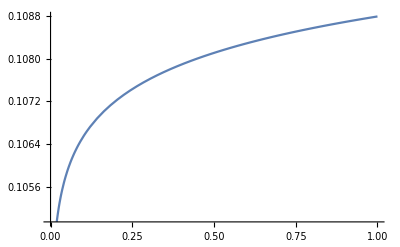

```mathematica
T=1000000000;
fullsysunstable={
y'[t]==(y*(piy-pi)/.{x->0,y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gy'[t]==(10000*((1-gy[t])*Qbdg-gy[t]*(1-Qgdg))*g/.{x->0,gx[t]->0,gx2[t]->0,y->y[t]}),
gz'[t]==(10000*((1-gz[t])*(Qbcg*g2+Qbdg*(g-g2))-gz[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)))/.{x->0,gx[t]->0,gx2[t]->0,y->y[t]}),
gy2'[t]==(10000*((gy[t]-gy2[t])*Qbdg-gy2[t]*(1-Qgdg))*g/.{x->0,gx[t]->0,gx2[t]->0,y->y[t]}),
gz2'[t]==(10000*((gz[t]-gz2[t])*(Qbcg*g2+Qbdg*(g-g2))-gz2[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)))/.{x->0,gx[t]->0,gx2[t]->0,y->y[t]})
};
{icgy,icgz,icgy2,icgz2}={gy[T],gz[T],gy2[T],gz2[T]}/.NDSolve[Join[repsysunstable/.{x->0,y->0.1},{gy[0]==0.5,gz[0]==0.5,gy2[0]==0.25,gz2[0]==0.25}],{gy,gz,gy2,gz2},{t,0,T}][[1]];
R=NDSolve[Join[fullsysunstable,{y[0]==0.1},{gy[0]==icgy,gz[0]==icgz,gy2[0]==icgy2,gz2[0]==icgz2}],{y,gy,gz,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",AccuracyGoal->20];
Plot[Evaluate[y[t]/.R[[1]]],{t,0,T}]
```

#### Heat maps

```mathematica
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* State 1: B ∅ B *)
(* State 2: B ∅ G *)
P2=0;
(* State 3: B -> B *)
(* State 4: B -> G *)
P42=(1-g)*ψ*e*g*ψ; 
P48=g*(1-ψ)*ϵ*g*ψ;
P4=FullSimplify[P48/(P42+P48)];
(* State 5: G ∅ B *)
(* State 6: G ∅ G *)
P62=(1-g)*(1-ψ)*(1-e)*g*ψ;
P68=g*ψ*(1-ϵ)*g*ψ;
P6=FullSimplify[P68/(P62+P68)];
(* State 7: G -> B *)
(* State 8: G -> G *)
P8=1;
ψ=0.5;
Qbdg=(1-e)*P2+e*P4;
Qbcg=ϵ*P4+(1-ϵ)*P2;
Qgdg=(1-e)*P6+e*P8;
Qgcg=ϵ*P8+(1-ϵ)*P6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

repsysBayes={
gx'[t]==((1-gx[t])*Qbcg-gx[t]*(1-Qgcg))*g,
gy'[t]==((1-gy[t])*Qbdg-gy[t]*(1-Qgdg))*g,
gz'[t]==(1-gz[t])*(Qbcg*g2+Qbdg*(g-g2))-gz[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)),
gx2'[t]==((gx[t]-gx2[t])*Qbcg-gx2[t]*(1-Qgcg))*g,
gy2'[t]==((gy[t]-gy2[t])*Qbdg-gy2[t]*(1-Qgdg))*g,
gz2'[t]==(gz[t]-gz2[t])*(Qbcg*g2+Qbdg*(g-g2))-gz2[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2))
};
fullsysBayes={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*((1-gx[t])*Qbcg-gx[t]*(1-Qgcg))*g/.{x->x[t],y->y[t]}),
gy'[t]==(100000*((1-gy[t])*Qbdg-gy[t]*(1-Qgdg))*g/.{x->x[t],y->y[t]}),
gz'[t]==(100000*((1-gz[t])*(Qbcg*g2+Qbdg*(g-g2))-gz[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)))/.{x->x[t],y->y[t]}),
gx2'[t]==(100000*((gx[t]-gx2[t])*Qbcg-gx2[t]*(1-Qgcg))*g/.{x->x[t],y->y[t]}),
gy2'[t]==(100000*((gy[t]-gy2[t])*Qbdg-gy2[t]*(1-Qgdg))*g/.{x->x[t],y->y[t]}),
gz2'[t]==(100000*((gz[t]-gz2[t])*(Qbcg*g2+Qbdg*(g-g2))-gz2[t]*((1-Qgcg)*g2+(1-Qgdg)*(g-g2)))/.{x->x[t],y->y[t]})
};

repsysNonreason={
gx'[t]==(ϵ-gx[t])*g,
gy'[t]==(e2-gy[t])*g,
gz'[t]==g*e2+g2*(ϵ-e2)-gz[t]*g,
gx2'[t]==(ϵ*gx[t]-gx2[t])*g,
gy2'[t]==(e2*gy[t]-gy2[t])*g,
gz2'[t]==gz[t]*(g*e2+g2*(ϵ-e2))-gz2[t]*g
};
fullsysNonreason={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(ϵ-gx[t])*g/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(e2-gy[t])*g/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(g*e2+g2*(ϵ-e2)-gz[t]*g)/.{x->x[t],y->y[t]}),
gx2'[t]==(100000*(ϵ*gx[t]-gx2[t])*g/.{x->x[t],y->y[t]}),
gy2'[t]==(100000*(e2*gy[t]-gy2[t])*g/.{x->x[t],y->y[t]}),
gz2'[t]==(100000*(gz[t]*(g*e2+g2*(ϵ-e2))-gz2[t]*g)/.{x->x[t],y->y[t]})
};

count=1;
basinBayesPsi25=Array[m,{100,3}];
basinBayesPsi5=Array[m,{100,3}];
basinBayesPsi75=Array[m,{100,3}];
basinNonreason=Array[m,{100,3}];

Do[
mysumBayesPsi25 = 0;
mysumBayesPsi5 = 0;
mysumBayesPsi75 = 0;
mysumNonreason= 0;

repsysBayesPsi25=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
fullsysBayesPsi25=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
repsysBayesPsi5=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
fullsysBayesPsi5=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
repsysBayesPsi75=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
fullsysBayesPsi75=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
repsys2=repsysNonreason/.{e1->ii/50,e2->jj/50};
fullsys2=fullsysNonreason/.{e1->ii/50,e2->jj/50};

Do[
{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsysBayesPsi25/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10,gx2[0]==25/100,gy2[0]==25/100,gz2[0]==25/100}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
RBayesPsi25=NDSolve[Join[fullsysBayesPsi25,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsysBayesPsi5/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10,gx2[0]==25/100,gy2[0]==25/100,gz2[0]==25/100}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
RBayesPsi5=NDSolve[Join[fullsysBayesPsi5,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsysBayesPsi75/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10,gx2[0]==25/100,gy2[0]==25/100,gz2[0]==25/100}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
RBayesPsi75=NDSolve[Join[fullsysBayesPsi75,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsys2/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10,gx2[0]==25/100,gy2[0]==25/100,gz2[0]==25/100}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
RNonreason=NDSolve[Join[fullsys2,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching"];

mysumBayesPsi25=mysumBayesPsi25+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi25[[1]]];
mysumBayesPsi5=mysumBayesPsi5+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi5[[1]]];
mysumBayesPsi75=mysumBayesPsi75+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi75[[1]]];
mysumNonreason=mysumNonreason+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RNonreason[[1]]];
,{i,1,4},{j,1,5-i}];
basinBayesPsi25[[count]]={ii/50,jj/50,mysumBayesPsi25/10};
basinBayesPsi5[[count]]={ii/50,jj/50,mysumBayesPsi5/10};
basinBayesPsi75[[count]]={ii/50,jj/50,mysumBayesPsi75/10};
basinNonreason[[count]]={ii/50,jj/50,mysumNonreason/10};
count=count+1;
,{ii,1,10},{jj,1,10}];

colfunc=(ColorData["SunsetColors"][Rescale[#,{0.6,0}]]&);

imageStprivateBayesPsi25=Show[ListDensityPlot[basinBayesPsi25,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","St abduction ψ=0.25"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageStprivateBayesPsi5=Show[ListDensityPlot[basinBayesPsi5,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","St abduction ψ=0.5"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageStprivateBayesPsi75=Show[ListDensityPlot[basinBayesPsi75,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","St abduction ψ=0.75"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageStprivateNonreason=Show[ListDensityPlot[basinNonreason,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","St non-reasoning"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
```

## Stern judging

### Public assessment

#### Ternary plot

```mathematica
(* ψ=0: w1=1/2, w4, w6=1/2, w7 *)
T=100000;
e1=0.01;
e2=0.01;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* State 1: B ∅ B *)
P12=(1-g)*ψ*(1-e)*g*(1-ψ); 
P13=(1-g)*ψ*(1-ϵ)*(1-g)*ψ; 
P15=g*(1-ψ)*(1-e)*(1-g)*ψ;
P1=Simplify[P15/(P12+P13+P15)];
(* State 2: B ∅ G *)
P2=0;
(* State 3: B -> B *)
P3=0;
(* State 4: B -> G *)
P42=(1-g)*ψ*e*g*ψ; 
P43=(1-g)*ψ*ϵ*(1-g)*(1-ψ);
P48=g*(1-ψ)*ϵ*g*ψ;
P4=Simplify[P48/(P42+P43+P48)];
(* State 5: G ∅ B *)
P5=1;
(* State 6: G ∅ G *)
P62=(1-g)*(1-ψ)*(1-e)*g*ψ;
P65=g*ψ*(1-e)*(1-g)*(1-ψ);
P68=g*ψ*(1-ϵ)*g*ψ;
P6=Simplify[(P65+P68)/(P62+P65+P68)];
(* State 7: G -> B *)
P73=(1-g)*(1-ψ)*ϵ*(1-g)*ψ;
P75=g*ψ*e*(1-g)*ψ;
P78=g*ψ*ϵ*g*(1-ψ);
P7=Simplify[(P75+P78)/(P73+P75+P78)];
(* State 8: G -> G *)
P8=1;
ψ=0.5;
Qbdb=(1-e)*P1+e*P3;
Qbdg=(1-e)*P2+e*P4;
Qbcb=ϵ*P3+(1-ϵ)*P1;
Qbcg=ϵ*P4+(1-ϵ)*P2;
Qgdb=(1-e)*P5+e*P7;
Qgdg=(1-e)*P6+e*P8;
Qgcb=ϵ*P7+(1-ϵ)*P5;
Qgcg=ϵ*P8+(1-ϵ)*P6;
repsys={
gx'[t]==Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t],
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t],
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,T}];
M[[count]]= {0.01*i,0.01*j,gx[T]/.R[[1]],gy[T]/.R[[1]],gz[T]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{10,2}];

count = 1;
Do[
{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsys/.{x->0.2*i,y->0.2*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,T}][[1]];
R=NDSolve[Join[fullsys,{x[0]==0.2*i,y[0]==0.2*j,gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Eqstable[[count]]= {Chop[x[T]/.R[[1]]],Chop[y[T]/.R[[1]]]};
count=count+1;
,{i,1,4},{j,1,5-i}];

(* Unstable equilibria *)
fullsysunstable={
y'[t]==(-y*(piy-pi)/.{x->0,y->y[t],gx[t]->0,gy->gy[t],gz->gz[t]}),
gy'[t]==(100000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->0,gx[t]->0,y->y[t]}),
gz'[t]==(100000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->0,gx[t]->0,y->y[t]})
};
repsysunstable={
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t]/.{gx[t]->0},
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]/.{gx[t]->0}
};
Equnstable=Array[m,{4,2}];

count = 1;
Do[
{icgy,icgz}={gy[T],gz[T]}/.NDSolve[Join[repsysunstable/.{x->0,y->0.2*i},{gy[0]==0.5,gz[0]==0.5}],{gy,gz},{t,0,T}][[1]];
R=NDSolve[Join[fullsysunstable,{y[0]==0.2*i,gy[0]==icgy,gz[0]==icgz}],{y,gy,gz},{t,0,T},Method->"StiffnessSwitching"];
Equnstable[[count]]= {0,Chop[y[T]/.R[[1]]]};
count=count+1;
,{i,1,4}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0.6565777137157706],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
image=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["public_stern_judging_psi05.pdf",image];
```

#### Heat maps

```mathematica
T=100000;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
(* State 1: B ∅ B *)
P12=(1-g)*ψ*(1-e)*g*(1-ψ); 
P13=(1-g)*ψ*(1-ϵ)*(1-g)*ψ; 
P15=g*(1-ψ)*(1-e)*(1-g)*ψ;
P1=Simplify[P15/(P12+P13+P15)];
(* State 2: B ∅ G *)
P2=0;
(* State 3: B -> B *)
P3=0;
(* State 4: B -> G *)
P42=(1-g)*ψ*e*g*ψ; 
P43=(1-g)*ψ*ϵ*(1-g)*(1-ψ);
P48=g*(1-ψ)*ϵ*g*ψ;
P4=Simplify[P48/(P42+P43+P48)];
(* State 5: G ∅ B *)
P5=1;
(* State 6: G ∅ G *)
P62=(1-g)*(1-ψ)*(1-e)*g*ψ;
P65=g*ψ*(1-e)*(1-g)*(1-ψ);
P68=g*ψ*(1-ϵ)*g*ψ;
P6=Simplify[(P65+P68)/(P62+P65+P68)];
(* State 7: G -> B *)
P73=(1-g)*(1-ψ)*ϵ*(1-g)*ψ;
P75=g*ψ*e*(1-g)*ψ;
P78=g*ψ*ϵ*g*(1-ψ);
P7=Simplify[(P75+P78)/(P73+P75+P78)];
(* State 8: G -> G *)
P8=1;
Qbdb=(1-e)*P1+e*P3;
Qbdg=(1-e)*P2+e*P4;
Qbcb=ϵ*P3+(1-ϵ)*P1;
Qbcg=ϵ*P4+(1-ϵ)*P2;
Qgdb=(1-e)*P5+e*P7;
Qgdg=(1-e)*P6+e*P8;
Qgcb=ϵ*P7+(1-ϵ)*P5;
Qgcg=ϵ*P8+(1-ϵ)*P6;

pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;

repsysBayes={
gx'[t]==Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t],
gy'[t]==Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t],
gz'[t]==Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t]
};
fullsysBayes={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(Qgcg*gx[t]*g+Qgcb*gx[t]*(1-g)+Qbcg*(1-gx[t])*g+Qbcb*(1-gx[t])*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(Qgdg*gy[t]*g+Qgdb*gy[t]*(1-g)+Qbdg*(1-gy[t])*g+Qbdb*(1-gy[t])*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(Qgcg*gz[t]*g+Qgdb*gz[t]*(1-g)+Qbcg*(1-gz[t])*g+Qbdb*(1-gz[t])*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};

repsysNonreason={
gx'[t]==ϵ*g+(1-ϵ)*(1-g)-gx[t],
gy'[t]==e2*g+(1-e2)*(1-g)-gy[t],
gz'[t]==ϵ*g+(1-e2)*(1-g)-gz[t]
};
fullsysNonreason={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100000*(ϵ*g+(1-ϵ)*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100000*(e2*g+(1-e2)*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100000*(ϵ*g+(1-e2)*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};

count=1;
basinBayesPsi25=Array[m,{100,3}];
basinBayesPsi5=Array[m,{100,3}];
basinBayesPsi75=Array[m,{100,3}];
basinNonreason=Array[m,{100,3}];

Do[
mysumBayesPsi25 = 0;
mysumBayesPsi5 = 0;
mysumBayesPsi75 = 0;
mysumNonreason= 0;

repsysBayesPsi25=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
fullsysBayesPsi25=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->25/100};
repsysBayesPsi5=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
fullsysBayesPsi5=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->5/10};
repsysBayesPsi75=repsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
fullsysBayesPsi75=fullsysBayes/.{e1->ii/50,e2->jj/50,ψ->75/100};
repsys2=repsysNonreason/.{e1->ii/50,e2->jj/50};
fullsys2=fullsysNonreason/.{e1->ii/50,e2->jj/50};

Do[
{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi25/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi25=NDSolve[Join[fullsysBayesPsi25,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi5/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi5=NDSolve[Join[fullsysBayesPsi5,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsysBayesPsi75/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RBayesPsi75=NDSolve[Join[fullsysBayesPsi75,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

{icgx,icgy,icgz}={gx[T],gy[T],gz[T]}/.NDSolve[Join[repsys2/.{x->2*i/10,y->2*j/10},{gx[0]==5/10,gy[0]==5/10,gz[0]==5/10}],{gx,gy,gz},{t,0,T}][[1]];
RNonreason=NDSolve[Join[fullsys2,{x[0]==2*i/10,y[0]==2*j/10},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz}],{x,y,gx,gy,gz},{t,0,T},Method->"StiffnessSwitching"];

mysumBayesPsi25=mysumBayesPsi25+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi25[[1]]];
mysumBayesPsi5=mysumBayesPsi5+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi5[[1]]];
mysumBayesPsi75=mysumBayesPsi75+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RBayesPsi75[[1]]];
mysumNonreason=mysumNonreason+Evaluate[x[T]+(x[T]*gx[T]+y[T]*gy[T]+(1-x[T]-y[T])*gz[T])*(1-x[T]-y[T])/.RNonreason[[1]]];
,{i,1,4},{j,1,5-i}];
basinBayesPsi25[[count]]={ii/50,jj/50,mysumBayesPsi25/10};
basinBayesPsi5[[count]]={ii/50,jj/50,mysumBayesPsi5/10};
basinBayesPsi75[[count]]={ii/50,jj/50,mysumBayesPsi75/10};
basinNonreason[[count]]={ii/50,jj/50,mysumNonreason/10};
count=count+1;
,{ii,1,10},{jj,1,10}];

colfunc=(ColorData["SunsetColors"][Rescale[#,{0.6,0}]]&);

imageSJpublicBayesPsi25=Show[ListDensityPlot[basinBayesPsi25,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SJ abduction ψ=0.25"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSJpublicBayesPsi5=Show[ListDensityPlot[basinBayesPsi5,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SJ abduction ψ=0.5"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSJpublicBayesPsi75=Show[ListDensityPlot[basinBayesPsi75,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SJ abduction ψ=0.75"}},BaseStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
imageSJpublicNonreason=Show[ListDensityPlot[basinNonreason,InterpolationOrder->0,PlotRange->{{0,0.2},{0,0.2},{0,0.6}},ColorFunction->colfunc,ColorFunctionScaling->False,ImageSize->Medium,AspectRatio->1,FrameLabel->{{"e_1",None},{"e_2","SJ non-reasoning"}},LabelStyle->Directive[FontSize->Large]],Frame->{{True,True},{True,True}}];
```

### Private assessment

#### Ternary plot

```mathematica
T=1000000;
e1=0.01;
e2=0.01;
ψ=0.5;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
(* State 1: B ∅ B *)
P12=(1-g)*ψ*(1-e)*g*(1-ψ); 
P13=(1-g)*ψ*(1-ϵ)*(1-g)*ψ; 
P15=g*(1-ψ)*(1-e)*(1-g)*ψ;
P1=Simplify[P15/(P12+P13+P15)];
(* State 2: B ∅ G *)
P2=0;
(* State 3: B -> B *)
P3=0;
(* State 4: B -> G *)
P42=(1-g)*ψ*e*g*ψ; 
P43=(1-g)*ψ*ϵ*(1-g)*(1-ψ);
P48=g*(1-ψ)*ϵ*g*ψ;
P4=Simplify[P48/(P42+P43+P48)];
(* State 5: G ∅ B *)
P5=1;
(* State 6: G ∅ G *)
P62=(1-g)*(1-ψ)*(1-e)*g*ψ;
P65=g*ψ*(1-e)*(1-g)*(1-ψ);
P68=g*ψ*(1-ϵ)*g*ψ;
P6=Simplify[(P65+P68)/(P62+P65+P68)];
(* State 7: G -> B *)
P73=(1-g)*(1-ψ)*ϵ*(1-g)*ψ;
P75=g*ψ*e*(1-g)*ψ;
P78=g*ψ*ϵ*g*(1-ψ);
P7=Simplify[(P75+P78)/(P73+P75+P78)];
(* State 8: G -> G *)
P8=1;
Qbdb=(1-e)*P1+e*P3;
Qbdg=(1-e)*P2+e*P4;
Qbcb=ϵ*P3+(1-ϵ)*P1;
Qbcg=ϵ*P4+(1-ϵ)*P2;
Qgdb=(1-e)*P5+e*P7;
Qgdg=(1-e)*P6+e*P8;
Qgcb=ϵ*P7+(1-ϵ)*P5;
Qgcg=ϵ*P8+(1-ϵ)*P6;

repsys={
gx'[t]==(1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)),
gy'[t]==(1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)),
gz'[t]==(1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)),
gx2'[t]==(gx[t]-gx2[t])*(Qbcg*g+Qbcb*(1-g))-gx2[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)),
gy2'[t]==(gy[t]-gy2[t])*(Qbdg*g+Qbdb*(1-g))-gy2[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)),
gz2'[t]==(gz[t]-gz2[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb*(1-2*g+g2))-gz2[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2))
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->i*0.01,y->j*0.01},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,20},Method->"StiffnessSwitching",AccuracyGoal->20];
M[[count]]= {0.01*i,0.01*j,gx[20]/.R[[1]],gy[20]/.R[[1]],gz[20]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(1000*((1-gx[t])*(Qbcg*g+Qbcb*(1-g))-gx[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy'[t]==(1000*((1-gy[t])*(Qbdg*g+Qbdb*(1-g))-gy[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz'[t]==(1000*((1-gz[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb(1-2*g+g2))-gz[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]}),
gx2'[t]==(1000*((gx[t]-gx2[t])*(Qbcg*g+Qbcb*(1-g))-gx2[t]*((1-Qgcg)*g+(1-Qgcb)*(1-g)))/.{x->x[t],y->y[t]}),
gy2'[t]==(1000*((gy[t]-gy2[t])*(Qbdg*g+Qbdb*(1-g))-gy2[t]*((1-Qgdg)*g+(1-Qgdb)*(1-g)))/.{x->x[t],y->y[t]}),
gz2'[t]==(1000*((gz[t]-gz2[t])*(Qbcg*g2+(Qbcb+Qbdg)*(g-g2)+Qbdb*(1-2*g+g2))-gz2[t]*((1-Qgcg)*g2+(2-Qgcb-Qgdg)*(g-g2)+(1-Qgdb)*(1-2*g+g2)))/.{x->x[t],y->y[t]})
};

Eqstable=Array[m,{10,2}];
count = 1;
Do[
{icgx,icgy,icgz,icgx2,icgy2,icgz2}={gx[T],gy[T],gz[T],gx2[T],gy2[T],gz2[T]}/.NDSolve[Join[repsys/.{x->0.2*i,y->0.2*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,T}][[1]];
R=NDSolve[Join[fullsys,{x[0]==0.2*i,y[0]==0.2*j},{gx[0]==icgx,gy[0]==icgy,gz[0]==icgz,gx2[0]==icgx2,gy2[0]==icgy2,gz2[0]==icgz2}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,T},Method->"StiffnessSwitching",InterpolationOrder->All];
Eqstable[[count]]= {x[T]/.R[[1]],y[T]/.R[[1]]};
count=count+1;
,{i,1,4},{j,1,5-i}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],PointSize[diskradius+thickness*2],Blue,Point[TernCoords[#1,#2]&@@@Eqstable]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
image=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["private_stern_judging_psi05.pdf",image];
```

## Heat maps

```mathematica
imagePublicHeatmaps=Legended[Multicolumn[{imageSSpublicBayesPsi25,imageStpublicBayesPsi25,imageSJpublicBayesPsi25,imageSSpublicBayesPsi5,imageStpublicBayesPsi5,imageSJpublicBayesPsi5,imageSSpublicBayesPsi75,imageStpublicBayesPsi75,imageSJpublicBayesPsi75,imageSSpublicNonreason,imageStpublicNonreason,imageSJpublicNonreason},{3,4}],Placed[BarLegend[{colfunc,{0,0.6}},LegendLayout->"Row",LegendMarkerSize->300,LabelStyle->{FontSize->Large},LegendFunction->"Frame",LegendMargins->5],Bottom]];
Export["public_heatmaps.pdf",imagePublicHeatmaps,ImageResolution->400,ImagePadding->0.01];

imagePrivateHeatmaps=Legended[Multicolumn[{imageSSprivateBayesPsi25,imageStprivateBayesPsi25,imageSSprivateBayesPsi5,imageStprivateBayesPsi5,imageSSprivateBayesPsi75,imageStprivateBayesPsi75,imageSSprivateNonreason,imageStprivateNonreason},{2,4}],Placed[BarLegend[{colfunc,{0,0.6}},LegendLayout->"Row",LegendMarkerSize->300,LabelStyle->{FontSize->Large},LegendFunction->"Frame",LegendMargins->5],Bottom]];
Export["private_heatmaps.pdf",imagePrivateHeatmaps,ImageResolution->400,ImagePadding->0.01];
```

```mathematica
imagePrivateHeatmaps=Legended[Multicolumn[{imageSSprivateBayesPsi25,imageStprivateBayesPsi25,imageSSprivateBayesPsi5,imageStprivateBayesPsi5,imageSSprivateBayesPsi75,imageStprivateBayesPsi75,imageSSprivateNonreason,imageStprivateNonreason},{2,4}],Placed[BarLegend[{colfunc,{0,0.6}},LegendLayout->"Row",LegendMarkerSize->300,LabelStyle->{FontSize->Large},LegendFunction->"Frame",LegendMargins->5],Bottom]];
Export["private_heatmaps.pdf",imagePrivateHeatmaps,ImageResolution->400,ImagePadding->0.01];
```